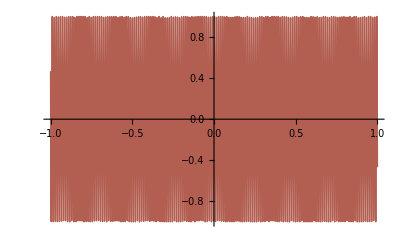

```mathematica
(* zad 1 *)
Plot[Sin[500 x],{x,-1,1},PlotStyle->Thick,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][x^2+y^2]],ColorFunctionScaling->False]
```

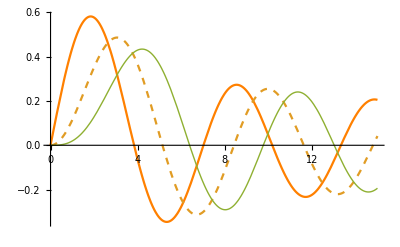

```mathematica
(* zad 2 *)
Plot[Evaluate@Table[BesselJ[n,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thick}]
```

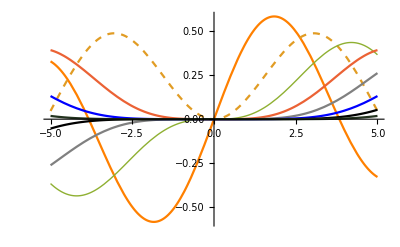

```mathematica
(* zad 3 *)
Plot[Evaluate@Table[BesselJ[n,x],{n,8}],{x,-5,5},PlotStyle->{Orange,Dashed,Thick,Glow,RGBColor[0.5,0.5,0.5],Blue,Black,Hue[0.3,0.4,0.2]}]
```

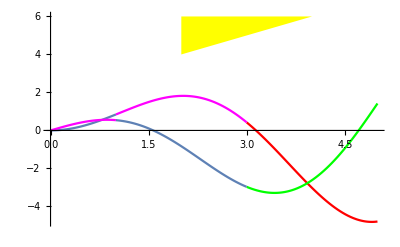

```mathematica
(* zad 4 *)
Show[
Plot[x Sin[x],{x,0,1}],
Plot[x Sin[x],{x,3,5},PlotStyle->Red],
Plot[x Sin[x],{x,1, 3},PlotStyle->Magenta],
Plot[x Cos[x],{x,0,1}, PlotStyle->Magenta],
Plot[x Cos[x],{x,3,5},PlotStyle->Green],
Plot[x Cos[x],{x,1, 3}],
Graphics[{Yellow,Polygon[{{2,4},{2,6},{4,6}}]}], PlotRange -> All]
```

```mathematica
(* zad 5 *)
GeoGraphics[{Red,
GeoPath[{FindGeoLocation[],
Entity["City",{"Sopot","Pomorskie","Poland"}], 
Entity["City",{"Gdynia","Pomorskie","Poland"}]},"Geodesic"]}]
```

-Graphics-